```mathematica
F[x_]:=30(x^2) (E^-Abs[x])
```

```mathematica
F[0]
```

0

```mathematica
F[-1]
```

30/ⅇ

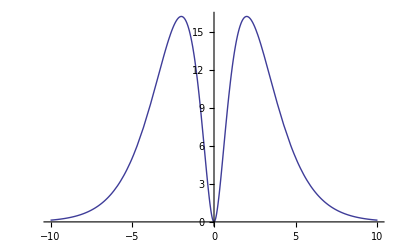

```mathematica
Plot[F[x], {x,-10,10}]
```

```mathematica
G[x_] := (x^3)(E^-Abs[Sqrt[x]])
```

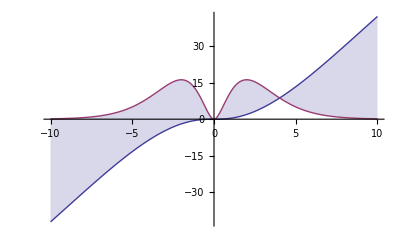

```mathematica
Plot[{G[x],F[x]},{x,-10,10}, {Filling -> {1->{2}}}]
```

```mathematica
Integrate[(F[x]-G[x]), {x, 0, 4}]
```

-(60 (13-1240 ⅇ^2+167 ⅇ^4))/ⅇ^4

```mathematica
Manipulate[Plot[Sin[a Cos[b x]], {x,0,2 Pi}], {{a,2,"Alpha Parameter"},0,20}, {{b,0, "Beta Parameter"},2,5}]
```

```mathematica
a x+b^2-c+2
```

2+b^2-c+a x

```mathematica
xxxx
```

xxxx

```mathematica
xx= b^2
```

b^2

```mathematica
xx^2
```

b^4

```mathematica
Plot3D[xx^2+Sqrt[Pi y]-y, {b,-5,5},{y,0,5}]
```

-Graphics3D-